InverseFunction::ifun: Inverse functions are being used. Values may be lost for multivalued inverses.

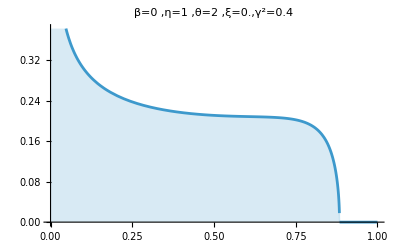

0.213332

```mathematica
ClearAll["Global`*"]
(*Global parameters case β=0*)
η=1;
θ=2;
γsquare= 0.4;
β=0;
ξ=0.0;
eps = 10^-16;
Which[ 
-γsquare<ξ<=0,
{ν=θ/η;
κ=γsquare-Abs[ξ];
m1=1/κ;
m2=Abs[ξ]/κ;
n1=γsquare-1;
n2=Abs[ξ];
ω=η;},
0<ξ<=1-γsquare,
{ν=θ/η;
κ=γsquare;
m1=1/κ;
m2=(ξ θ)/(κ η);
n1=0;
n2=1-γsquare -ξ;
ω=η;},
1-γsquare<ξ<1,
{ν=η/θ;
κ=1-ξ;
m1=1/κ;
m2=ξ/κ;
n1=1-γsquare -ξ;
n2=0;
ω=θ;}
];
(* Final part for plots*)
m1tilde=m1(n2-n1);
s0=(1+m1tilde)/(ν(1+m2));
c0=((m1tilde ν+ν+m2)*((m2+1)/(m1tilde ν+ν+m2+1))^(1/ν+1))/(m2+1);

c1=(ν*(m1tilde+1)*((m2+1)/(m1tilde ν+ν+m2+1))^(1/ν-1))/(m1tilde ν+ν+m2+1)^2;
J[s_] = (c0+c1* s)((1+s)/s)^(1/ν);
II[s_]=InverseFunction[J][s];
sa=-((ν-1)/(2 ν))-(1/(2 ν c1))*Sqrt[4 c0 c1 ν+c1^2 (ν-1)^2];
sb=-((ν-1)/(2 ν))+(1/(2 ν c1))*Sqrt[4 c0 c1 ν+c1^2 (ν-1)^2];
a=Re[J[sa]];
b=Re[J[sb]];
μ[x_]=Abs[((m2+1)*(m1tilde ν+ν+m2+1))/(ν*(m1tilde+1)*π*x)*Im[1/(s0-II[x])]]*Boole[a<=x<=b];

Plot[ω x^(ω-1)μ[x^ω],{x,0,1},PlotRange->{{0,1},Automatic},Filling->Bottom,PlotLabel->Style[",ξ="<>ToString[ξ]<>",γ^2="<>ToString[γsquare]",η="<>ToString[η]",θ="<>ToString[θ]"β="<>ToString[β],FontSize->22,Black]]
NIntegrate[μ[x],{x,0,1}]
```

InverseFunction::ifun: Inverse functions are being used. Values may be lost for multivalued inverses.

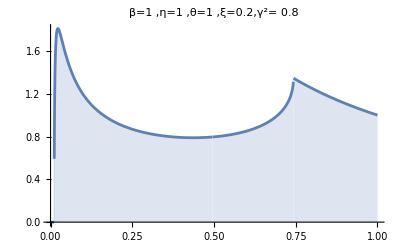

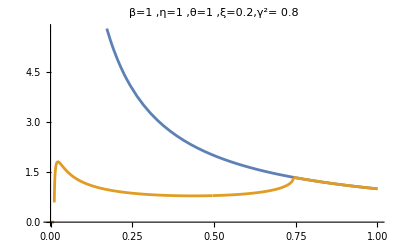

```mathematica
(*Global parameters case β>0*)
ClearAll["Global`*"]
η=1;
θ=1;
γsquare= 0.8;
βtilde=1/η;
β= βtilde* η;
ξ=1-γsquare;
eps = 10^-16;
ν=θ/η;
κ=γsquare;
m1=0;
m2=(ξ θ)/(κ η);
Subscript[m, 2]=m2;
n1=0;
n2=1-γsquare -ξ;
ω=η;
c0=ⅇ^(-(β (1+Subscript[m, 2]))/ν) (-1+ⅇ^(β (1+Subscript[m, 2])))^(2/ν) (-1+ⅇ^(β (1+ν+Subscript[m, 2])))^(-(2+ν)/ν) (-ⅇ^((β (1+ν+Subscript[m, 2]))/ν) ((-1+ⅇ^(β (1+ν+Subscript[m, 2])))/(-1+ⅇ^(β (1+Subscript[m, 2]))))^(1/ν)+ⅇ^(β (1+ν+Subscript[m, 2])) ((ⅇ^(β (1+Subscript[m, 2])) (-1+ⅇ^(β (1+ν+Subscript[m, 2]))))/(-1+ⅇ^(β (1+Subscript[m, 2]))))^(1/ν));
c1=-ⅇ^(-(β (1+Subscript[m, 2]))/ν) (-1+ⅇ^(β (1+Subscript[m, 2])))^(-1+2/ν) (ⅇ^(β (1+Subscript[m, 2]))-ⅇ^(β (1+ν+Subscript[m, 2]))) (-1+ⅇ^(β (1+ν+Subscript[m, 2])))^(-(2+ν)/ν) (ⅇ^((β (1+ν+Subscript[m, 2]))/ν) ((-1+ⅇ^(β (1+ν+Subscript[m, 2])))/(-1+ⅇ^(β (1+Subscript[m, 2]))))^(1/ν)-((ⅇ^(β (1+Subscript[m, 2])) (-1+ⅇ^(β (1+ν+Subscript[m, 2]))))/(-1+ⅇ^(β (1+Subscript[m, 2]))))^(1/ν));
I11=(ⅇ^(β (1+ν+Subscript[m, 2])) (-1+ⅇ^(β (1+Subscript[m, 2]))))/(-ⅇ^(β (1+Subscript[m, 2]))+ⅇ^(β (1+ν+Subscript[m, 2])));
I21=-(1-ⅇ^(β (1+Subscript[m, 2])))/(-ⅇ^(β (1+Subscript[m, 2]))+ⅇ^(β (1+ν+Subscript[m, 2])));
J[s_] = (c0+c1* s)((1+s)/s)^(1/ν);
II[s_]=InverseFunction[J][s];
sa=-((ν-1)/(2 ν))-(1/(2 ν c1))*Sqrt[4 c0 c1 ν+c1^2 (ν-1)^2];
sb=-((ν-1)/(2 ν))+(1/(2 ν c1))*Sqrt[4 c0 c1 ν+c1^2 (ν-1)^2];
a=Re[J[sa]];
b=Re[J[sb]];
μ[x_]= 1/(π β x)Abs[Arg[I11-II[x]] - Arg[I21 - II[x]]]*Boole[a<=x<=1];
Plot[ω x^(ω-1)μ[x^ω],{x,0,1},PlotRange->{{0,1},Automatic},Filling->Bottom,PlotLabel->Style[",ξ="<>ToString[ξ]<>",γ^2= "<>ToString[γsquare]",η="<>ToString[η]",θ="<>ToString[θ]"β="<>ToString[βtilde],FontSize->22,Black]]
Plot[{1/(βtilde x),ω x^(ω-1)μ[x^ω]},{x,0,1},PlotRange->{{0,1},Automatic},PlotLabel->Style[",ξ="<>ToString[ξ]<>",γ^2= "<>ToString[γsquare]",η="<>ToString[η]",θ="<>ToString[θ]"β="<>ToString[βtilde],FontSize->22,Black]]
```

## 3D module

$Aborted

InverseFunction::ifun: Inverse functions are being used. Values may be lost for multivalued inverses.

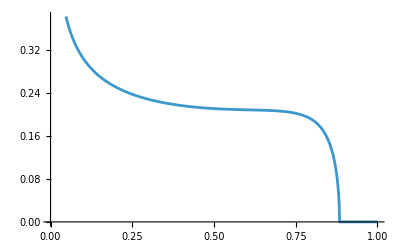

```mathematica
ClearAll["Global`*"]
(*Global parameters*)
η=1;
θ=2;
γsquare=0.4;
β=0;
eps=10^-16;

(*Define a function that calculates the density for a given x and ξ*)
density3D[xVal_?NumericQ,ξVal_?NumericQ]:=Module[{ν,κ,m1,m2,n1,n2,ω,m1tilde,s0,c0,c1,J,invJ,sa,sb,a,b,xTransformed,val,dens},(*1. Determine parameters based on the region of ξ*)Which[-γsquare<ξVal<=0,{ν=θ/η;
κ=γsquare-Abs[ξVal];
m1=1/κ;
m2=Abs[ξVal]/κ;
n1=γsquare-1;
n2=Abs[ξVal];
ω=η;},0<ξVal<=1-γsquare,{ν=θ/η;
κ=γsquare;
m1=1/κ;
m2=(ξVal θ)/(κ η);
n1=0;
n2=1-γsquare-ξVal;
ω=η;},1-γsquare<ξVal<1,{ν=η/θ;
κ=1-ξVal;
m1=1/κ;
m2=ξVal/κ;
n1=1-γsquare-ξVal;
n2=0;
ω=θ;}];
(*2. Calculate Derived Constants*)m1tilde=m1 (n2-n1);
s0=(1+m1tilde)/(ν (1+m2));
c0=((m1tilde ν+ν+m2)*((m2+1)/(m1tilde ν+ν+m2+1))^(1/ν+1))/(m2+1);
c1=(ν*(m1tilde+1)*((m2+1)/(m1tilde ν+ν+m2+1))^(1/ν-1))/(m1tilde ν+ν+m2+1)^2;
(*3. Define J locally so it uses the current c0,c1,ν*)J[s_]=(c0+c1*s) ((1+s)/s)^(1/ν);
(*4. Calculate Critical Points and Support Bounds*)(*Using the discriminant formula from your code*)sa=-((ν-1)/(2 ν))-(1/(2 ν c1))*Sqrt[4 c0 c1 ν+c1^2 (ν-1)^2];
sb=-((ν-1)/(2 ν))+(1/(2 ν c1))*Sqrt[4 c0 c1 ν+c1^2 (ν-1)^2];
a=Re[J[sa]];
b=Re[J[sb]];
xTransformed=xVal^ω;
(*5. Calculate Density*)(*Check if x is within the support[a,b]*)If[a<=xTransformed<=b,(*Calculate Inverse Function numerically for the current point*)invJ=InverseFunction[J][xTransformed];
dens=Abs[((m2+1)*(m1tilde ν+ν+m2+1))/(ν*(m1tilde+1)*π*xTransformed)*Im[1/(s0-invJ)]];
(*Apply the Jacobian scaling:ω x^(ω-1)*)ω xVal^(ω-1)*dens,0 (*Return 0 if outside support*)]];

(*Create the 3D Plot*)
(*Range of ξ is set slightly inside boundaries to avoid numerical singularities*)
```

#### Trying to parallelize the code

```mathematica
ClearAll["Global`*"]
(*---1. Define Parameters and the Function---*)
η=1;
θ=2;
γsquare=0.4;
β=0;
eps=10^-16;

(*Define the density function*)
density3D[xVal_?NumericQ,ξVal_?NumericQ]:=Module[{ν,κ,m1,m2,n1,n2,ω,m1tilde,s0,c0,c1,J,invJ,sa,sb,a,b,xTransformed,dens},Which[-γsquare<ξVal<=0,{ν=θ/η;κ=γsquare-Abs[ξVal];
m1=1/κ;m2=Abs[ξVal]/κ;
n1=γsquare-1;n2=Abs[ξVal];ω=η;},0<ξVal<=1-γsquare,{ν=θ/η;κ=γsquare;m1=1/κ;
m2=(ξVal θ)/(κ η);n1=0;
n2=1-γsquare-ξVal;ω=η;},1-γsquare<ξVal<1,{ν=η/θ;κ=1-ξVal;m1=1/κ;
m2=ξVal/κ;n1=1-γsquare-ξVal;n2=0;
ω=θ;}];
m1tilde=m1 (n2-n1);
s0=(1+m1tilde)/(ν (1+m2));
c0=((m1tilde ν+ν+m2)*((m2+1)/(m1tilde ν+ν+m2+1))^(1/ν+1))/(m2+1);
c1=(ν*(m1tilde+1)*((m2+1)/(m1tilde ν+ν+m2+1))^(1/ν-1))/(m1tilde ν+ν+m2+1)^2;
J[s_]=(c0+c1*s) ((1+s)/s)^(1/ν);
sa=-((ν-1)/(2 ν))-(1/(2 ν c1))*Sqrt[4 c0 c1 ν+c1^2 (ν-1)^2];
sb=-((ν-1)/(2 ν))+(1/(2 ν c1))*Sqrt[4 c0 c1 ν+c1^2 (ν-1)^2];
a=Re[J[sa]];
b=Re[J[sb]];
xTransformed=xVal^ω;
Quiet[If[a<=xTransformed<=b,invJ=InverseFunction[J][xTransformed];
dens=Abs[((m2+1)*(m1tilde ν+ν+m2+1))/(ν*(m1tilde+1)*π*xTransformed)*Im[1/(s0-invJ)]];
ω xVal^(ω-1)*dens,0.]]];

(*---2. Parallel Data Generation---*)
DistributeDefinitions[density3D,η,θ,γsquare,β,eps];

gridPoints=400;
xiStart=-γsquare+0.005;
xiEnd=1-0.005;

Print["Generating data grid..."];
rawData=Flatten[ParallelTable[{xiVal,xVal,density3D[xVal,xiVal]},{xiVal,xiStart,xiEnd,(xiEnd-xiStart)/gridPoints},{xVal,0,1,1/gridPoints},Method->"FinestGrained"],1];

(*---3. Clean Data---*)
(*Removing invalid points to prevent holes*)
cleanData=Select[rawData,NumericQ[Last[#]]&];

(*---4. Color Function (Weighted& Clamped at 10)---*)
myColorFunc=Function[z,ColorData["SunsetColors"][(Min[z,10.0]/10.0)^0.5]];

(*---5. Visualization (No White Background)---*)
plotHeatmap=ListDensityPlot[cleanData,ColorFunction->"SolarColors",ColorFunctionScaling->False,PlotLegends->BarLegend[{myColorFunc,{0,12}},LegendLabel->"Density"],FrameLabel->{Style["ξ",14,Italic],Style["x",14,Italic]},PlotLabel->Style["Top View (Heatmap)",16],ImageSize->Medium,PlotRangePadding->None,Background->None (*Transparent*)];

plot3D=ListPlot3D[cleanData,ColorFunction->"SolarColors",Mesh->None,AxesLabel->{Style["ξ",14,Italic],Style["x",14,Italic],Style["Density",14]},PlotLabel->Style["3D Surface View",16],ImageSize->Medium,PlotRange->{0,15},BoxRatios->{1,1,0.4},Background->None (*Transparent*)];

Row[{plotHeatmap,plot3D}]
```

Generating data grid...

-Graphics--Graphics3D-

-Graphics--Graphics3D-

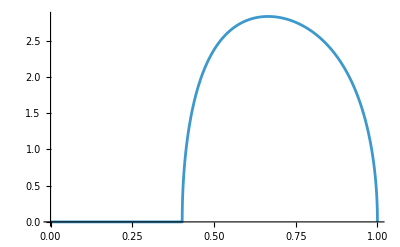

```mathematica
Plot[density3D[x,0.61],{x,0,1},PlotRange->All]
Manipulate[Plot[density3D[x,t],{x,0,1},PlotRange->All],{t,0.5,0.7}]
```

```mathematica
cleanData=Select[rawData,NumericQ[Last[#]]&];

(*1. Define the Color Logic separately*)(*z is the density value.Exp[-Abs[z]] maps 0 to 1 (Yellow) and High Values to 0 (Blue).*)colorLogic=Function[z,ColorData["TemperatureMap"][1-Exp[-Abs[z/3]]]];

(*2. Create the Plot with the matched Legend*)
ListPlot3D[cleanData,(*Use the custom logic defined above*)ColorFunction->Function[{x,y,z},colorLogic[z]],ColorFunctionScaling->False,(*Visual Settings*)Mesh->10,BoxRatios->{1,1,0.4},(*Keeps it flat*)PlotRange->{0,8},(*Cuts off spikes above 15*)Background->None,(*Transparent*)(*Labels*)AxesLabel->{Style["ξ",16,Italic,Black],Style["x",16,Italic,Black],None},PlotLabel->Style["Density Evolution μ[x]",18,Black],(*THE LEGEND:We pass the SAME'colorLogic' and the range {0,15}*)PlotLegends->BarLegend[{colorLogic,{0,8}},LegendLabel->Style["Density",12],LegendMarkerSize->300 (*Height of the bar*)]]
```

-Graphics3D-